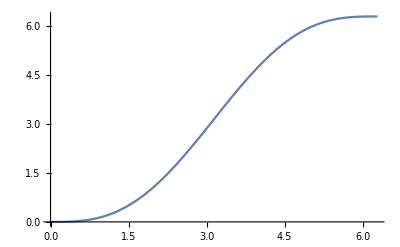

```mathematica
Plot[x-Sin[x],{x,0,2π}]
```

```mathematica
obj[x_]:=(rt-xt[x]*a)*(r-at*x)
```

```mathematica
lag[x_]:=obj[x]-λt*x+γ*(v1-xt[x]*v1)
```

```mathematica
D[lag[x],x]
```

```mathematica
-λt-at (rt-a xt[x])-a (r-at x) xt'[x]-v1 γ xt'[x]/.xt'[x]->v1t
```

```mathematica
-a v1t (r-at x)-v1 v1t γ-λt-at (rt-a xt[x])//FullSimplify
```

at (-rt+a v1t x)-v1t (a r+v1 γ)-λt+a at xt[x]